## De Boor algorithm

The next cell evaluates the de Boor algorithm:

For r=n, d_0^n(u) is the point corresponding to parameter value u on the B-spline curve defined by d_1, ..., d_(n+ll-1).

```mathematica
(SetDirectory[ToFileName[Extract["FileName"/.NotebookInformation[EvaluationNotebook[]],{1},FrontEnd`FileName]]];)

db[r_,i_,u_]:=(
(* Print["db input: r=",r," i=",i," u=",u]; *)
If [r==0,point = dd[[i]],point = ((knot[[i+n-r+1]]-u)*db[r-1,i-1,u]+(u-knot[[i]])*db[r-1,i,u])/(knot[[i+n-r+1]]-knot[[i]])];

t1 = (n+1) - (ii - i);
t2 = r + 1; 
intermdeboor[[t1,t2]] = point;
(*Print["map into table: (i,r)=",i," ",r," goes to ",t1," ",t2]; *)
(* Print["db return point=",point]; *)
Return[point];
);
```

```mathematica
evaluatedb[n_, u_]:= (
j = n+1;
While[(knot[[j]]≤    u ) && (j ≤ numknots-n - 1),j++];
ii = j-1; (* u's interval *)
(* Print["parameter u= ",u," is in interval ",ii]; *)

point = db[n,ii,u];
Return[point]
);
```

## Input control polygon and knot vector

```mathematica
n=3;
dd={{0,0.5},{-1,0},{-2,1.5},{-1,3},{2,3},{2.2,1},{2.9,1},{3,3},{6,2},{7,1}};

knot={0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1};
knot={0,0,0,0,1,1.5,2,2.5,3,3.5,4,4,4,4};
(*knot={0,0,0,0,0,0,1,2,3,4,5,5,5,5,5,5};*)

(* One Cubic example *)
(*
n=3;
dd={{0,0},{1,1},{2,0}, {3,2}};
knot={0,0,0,0,1,1,1,1};
*)
(* One Quadratic example *)
(*
n=2;
dd={{0,0},{1,1},{2,0}};
knot={0,0,0,1,1,1};
*)
numknots=Length[knot];

(* Structure to hold all intermediate deboor points *)
intermdeboor = Table[{0,0},{i,1,n+1},{j,1,n+1}];
levels = Table[{0},{i,1,n+1}];
```

## Evaluate and Plot

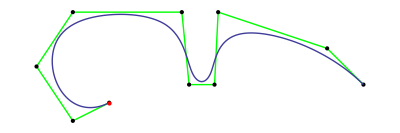

```mathematica
curve=ParametricPlot[evaluatedb[n,u],{u,knot[[n+1]],knot[[numknots-n]]}, PlotStyle->{Thick}]; 

poly=Graphics[{Thick,Green,Line[dd]}];
points=Graphics[{PointSize[Large],Point[dd]}];
begin= Graphics[{PointSize[Large],Red,Point[dd[[1]]]}];
Show[{poly,points, curve, begin}]
```

## Dynamic deBoor -- Nested polygons

```mathematica
createlevels[u_] := (
evaluatedb[n,u];
(* Point on curve *)
levels[[n+1]] = Graphics[{RGBColor[1.0, 0.3, 0.3],PointSize[Large],Point[intermdeboor[[n+1,n+1]]]}];

Do[(
(* set variable color based on level *)
t = l/(n+1); 
(* load control points to connect with a line *)
myline = Table[{0,0},{j,1,n -l+2}];
Do[myline[[j]] = intermdeboor[[l+j-1,l]],{j,1,n -l+2}];

levels[[l]] = Graphics[{RGBColor[0.2 + t*0.9, 0.5, 0.5], Thick,  Line[{myline}], PointSize[Large],Point[{myline}]}]),
{l,n,2,-1}];

(* dummy -- we want points from original control poly *)
levels[[1]] = Graphics[{RGBColor[1.0, 0.3, 0.3],PointSize[Large],Point[intermdeboor[[n+1,n+1]]]}];
);
```

```mathematica
curve=ParametricPlot[evaluatedb[n,u],{u,knot[[n+1]],knot[[numknots-n]]}, PlotStyle->{Thick}]; 

poly=Graphics[{Thick,Green,Line[dd]}];
points=Graphics[{PointSize[Large],Point[dd]}];
begin= Graphics[{PointSize[Large],Red,Point[dd[[1]]]}];

domainu1 = knot[[n+1]];
domainu2 = knot[[numknots -n]];
 
Manipulate[
(createlevels[u];
Show[{poly,curve,points, levels}]),
{u,domainu1, domainu2}]

Manipulate[
(createlevels[u];
Show[{poly,curve,points, levels[[2]]}]),
{u,domainu1, domainu2}]
```

```mathematica
createlevels[0.7];
Show[{poly,curve,points, levels[[2]]}]
(*Export["knotinsert_nonic.eps",%]*)
```

-Graphics-